```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
$TrialsDir = "../../../runs/Trials";
```

```mathematica
data = Import[$TrialsDir<>"/N5K9/24788149.dat"];
```

```mathematica
changeNK[5, 9];
```

```mathematica
cmatdata = cMatOne/@data;
```

```mathematica
eig = Flatten[Eigenvalues/@Flatten[cmatdata[[All, 2;;$K+1]], 1]];
```

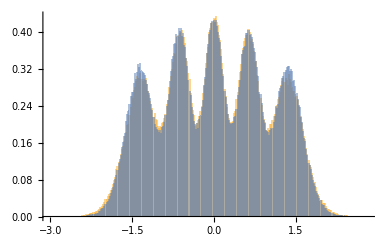

```mathematica
Histogram[{eig/StandardDeviation[eig], randeig/StandardDeviation[randeig]}, 300, PDF]
```

```mathematica
randmats = (# - 1/($N)Tr[#]IdentityMatrix[$N])&/@RandomVariate[GaussianUnitaryMatrixDistribution[1, $N], $K*Length[data]];
```

```mathematica
randeig = Flatten[Eigenvalues/@randmats];
```

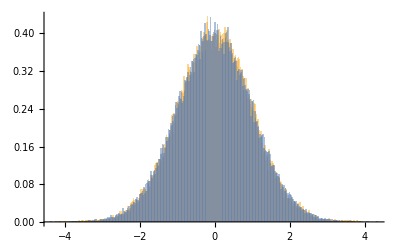

```mathematica
Histogram[{Standardize[Re/@Flatten[cmatdata[[All, 2;;, 1, 1]]]], Standardize[Re/@randmats[[All, 1, 1]]]}, 400 ,PDF]
```

```mathematica
σ = StandardDeviation[eig]/StandardDeviation[randeig];
```

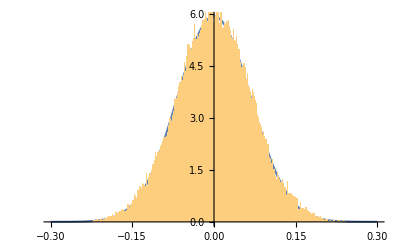

```mathematica
Show[
Plot[1/(√π σ)Exp[-1/σ^2 x^2], {x, -0.3, 0.3}],
Histogram[Re/@Flatten[cmatdata[[All,2;;, 2, 3]]], 400 ,PDF]
]
```